```mathematica
(*This notebook contains the differential equation describing the motion of single pendulum in a non inertial reference system. *)
(*Here 'l' represents the length of the pendulum arm, 'a' is the acceleration of the non inertial system and 'g' is acceleration of free fall.*)
l = 0.1;a=6.7; g=9.8;
NDSolve[{y''[x]==a/l*Cos[y[x]]-g/l*Sin[y[x]],y[0]==0,y'[0]==0},y,{x,0,10}]
```

{{y→InterpolatingFunction[{{0., 10.}}, <>]}}

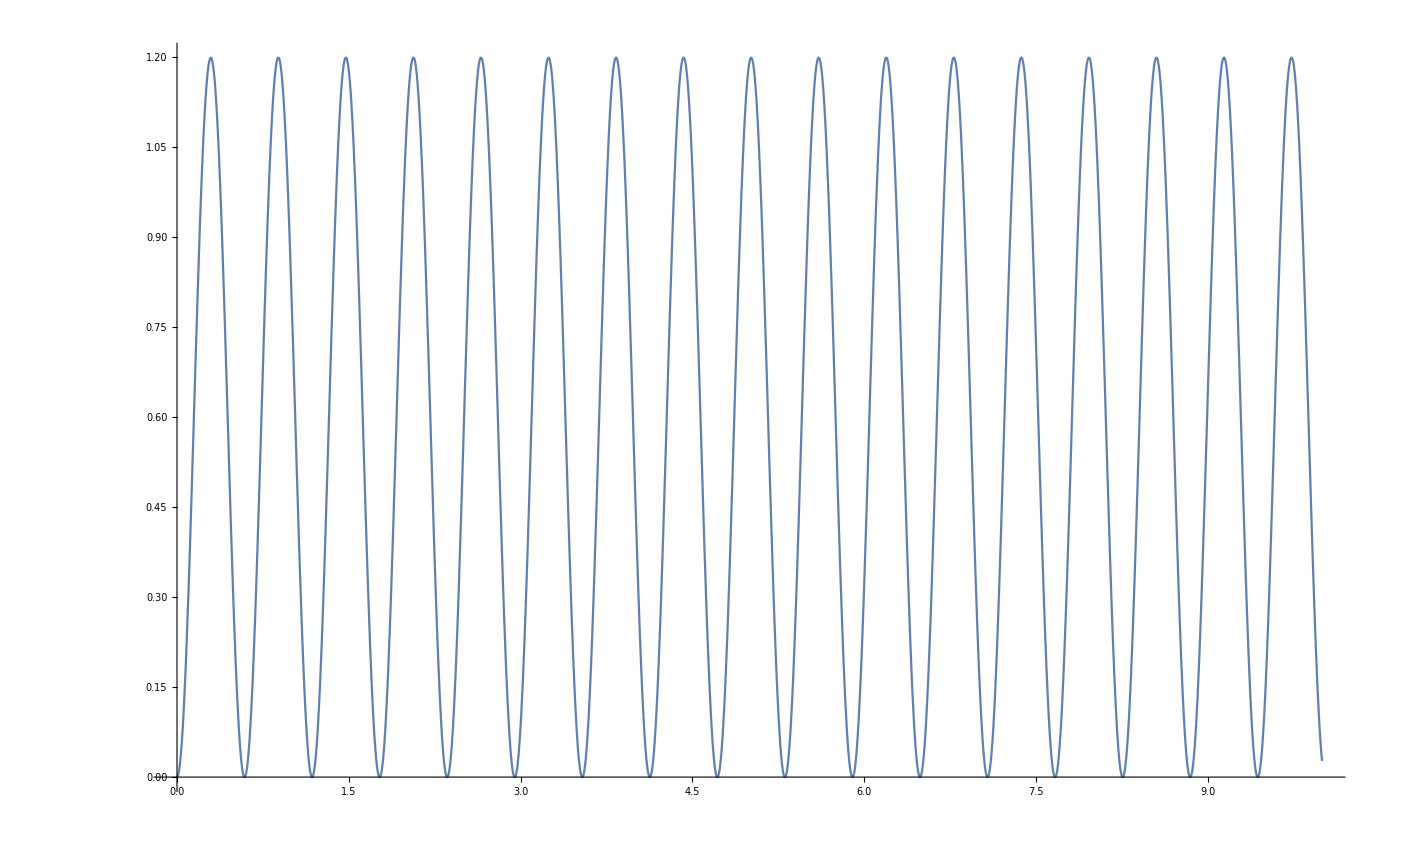

```mathematica
Plot[Evaluate[y[x]/.%],{x,0,10}]
```